```mathematica
(*P50 HW5*)
(*Each question is worth 1 pt. You can type your answer directly below the questions. Please upload your solution in .nb or .pdf*)


(*Midterm review problems:*)
```

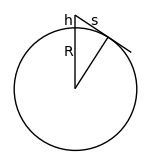
```mathematica
(*Q1:If you are at the top of a tower of height h above the surface of the earth,show that the distance you can see along the surface of the earth is,to first order in h,s=√(2 R h),where R is the radius of the earth.Use the fact that h<<R.Come up with a formula that gives the distance to the horizon in miles for a given h measured in feet.How far can you see from the deck of a boat 10 feet above the surface?How far can you see from an airplane at 30,000 feet?
-Graphics-
Write the Pythagorean theorem for the triangle in the picture.Solve for s,the distance we can see.
*)
```

```mathematica
Solve[R^2+s^2==(R+h)^2,s]//Flatten
Series[s/.%[[2]],{h,0,1}]
R=3958.761;
Sqrt[2*R*10*1/5280]
Sqrt[2*R*30000*1/5280]
```

{s→-√h √(h+2 R),s→√h √(h+2 R)}

√2 √R √h+O[h]^(3/2)

3.87238

212.099

```mathematica
(*Q2: Use row reduce to solve the following equations: 
{y+x Cos[θ],x+z+2 y Cos[θ],y+2 z Cos[θ]}=={0,Cos[3 θ],Cos[3 θ]} *)
```

```mathematica
RowReduce[({{Cos[θ], 1, 0, 0}, {1, 2Cos[θ], 1, Cos[3θ]}, {0, 1, 2Cos[θ], Cos[3θ]}})]//MatrixForm//Simplify
```

(1 | 0 | 0 | 1-2 Cos[θ]
0 | 1 | 0 | 1-Cos[θ]+Cos[2 θ]
0 | 0 | 1 | -2 (1+2 Cos[θ]) Sin[θ/2]^2)

```mathematica
(*W5 problems:*)
```

```mathematica
(*Q3: The set of 2x2 matrices is a linear space(zero matrix exists,multiplication by a scalar is well defined,the sum of two matrices is a matrix,etc). What is the dimension of this space? *)
```

```mathematica
(* Matrix 2x2 basis ({{1, 0}, {0, 0}}),({{0, 1}, {0, 0}}),({{0, 0}, {1, 0}}),({{0, 0}, {0, 1}}) so dimension of linear space is 4. *)
```

```mathematica
(*Q4: In 3D space, our basis is Eb = {{1,0,0}, {0,1,0},{0,0,1}}, i.e. unit vectors along x, y and z. What is the matrix TE for the following linear transformation: Rotate along x axis for θ, then perform mirror imagine of x-y plane, then rotate along z axis for θ. *)
(*Solution:*)
```

```mathematica
M = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
TE1=RotationMatrix[θ,{1,0,0}].M
TE1//MatrixForm
```

{{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

```mathematica
TE2=TE1.ReflectionMatrix[{0,0,1}]
TE2//MatrixForm
```

{{1,0,0},{0,Cos[θ],Sin[θ]},{0,Sin[θ],-Cos[θ]}}

(1 | 0 | 0
0 | Cos[θ] | Sin[θ]
0 | Sin[θ] | -Cos[θ])

```mathematica
TE = RotationMatrix[θ,{0,0,1}].TE2
TE//MatrixForm
```

{{Cos[θ],-Cos[θ] Sin[θ],-Sin[θ]^2},{Sin[θ],Cos[θ]^2,Cos[θ] Sin[θ]},{0,Sin[θ],-Cos[θ]}}

(Cos[θ] | -Cos[θ] Sin[θ] | -Sin[θ]^2
Sin[θ] | Cos[θ]^2 | Cos[θ] Sin[θ]
0 | Sin[θ] | -Cos[θ])

```mathematica
(*Q5: Following Q4, let's now use a different basis eb = {{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}}, i.e. rotated along z axis by θ. What is the new transformation matrix Te in this basis?*)
(*Solution*)
```

```mathematica
eb=({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}});
Te=Transpose[eb].TE.eb
Te//MatrixForm//Simplify
```

{{2 Cos[θ]^2 Sin[θ]^2+Cos[θ] (Cos[θ]^2-Sin[θ]^2),-2 Cos[θ]^3 Sin[θ]+Sin[θ] (Cos[θ]^2-Sin[θ]^2),-2 Cos[θ] Sin[θ]^2},{2 Cos[θ]^2 Sin[θ]-Sin[θ] (Cos[θ]^3-Cos[θ] Sin[θ]^2),2 Cos[θ] Sin[θ]^2+Cos[θ] (Cos[θ]^3-Cos[θ] Sin[θ]^2),Cos[θ]^2 Sin[θ]-Sin[θ]^3},{-Sin[θ]^2,Cos[θ] Sin[θ],-Cos[θ]}}

(1/2 Cos[θ] (Cos[θ]+2 Cos[2 θ]-Cos[3 θ]) | Sin[θ] (Cos[θ]^2-2 Cos[θ]^3-Sin[θ]^2) | -2 Cos[θ] Sin[θ]^2
-1/2 (-2 Cos[θ]+Cos[2 θ]) Sin[2 θ] | 1/2 Cos[θ] (2+Cos[θ]-2 Cos[2 θ]+Cos[3 θ]) | Cos[2 θ] Sin[θ]
-Sin[θ]^2 | Cos[θ] Sin[θ] | -Cos[θ])

```mathematica
(*Q6: In class, we see that for the linear space of the set polynomials in a variable x of degree≤3, one basis we can use is: 
B1=1
B2=x
B3=x^2
B4=x^3
And the matrix for differentiation transformation is DmatB = ({{0, 1, 0, 0}, {0, 0, 2, 0}, {0, 0, 0, 3}, {0, 0, 0, 0}}).
If we use a different basis: 
b1=1
b2=1+x
b3=1+x^2
b4=1+x^3
What is the matrix for differentiation transformation Dmat?
*)
```

```mathematica
D[1,x]
D[1+x,x]
D[1+x^2,x]
D[1+x^3,x]
```

0

1

2 x

3 x^2

```mathematica
mat=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 2, 0, 0}, {0, 0, 3, 0}});
Dmat=Transpose[mat]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 3
0 | 0 | 0 | 0)